```mathematica
$Assumpitons:=a∈Reals&&a>0&&b∈Reals&&b>0
Solve[{r*x+(a)*y==x^3, r*y+(-a)*x==y^3}, {x, y}]//Simplify
```

{{x→0,y→0},{x→-1/2 √(3 r-√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2)))),y→(√(3 r-√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2)))) (r+√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2)))))/(8 a)},{x→1/2 √(3 r-√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2)))),y→-(√(3 r-√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2)))) (r+√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2)))))/(8 a)},{x→-1/2 √(3 r-√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2)))),y→((r+√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2)))) √(3 r-√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2)))))/(8 a)},{x→1/2 √(3 r-√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2)))),y→-((r+√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2)))) √(3 r-√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2)))))/(8 a)},{x→-1/2 √(3 r+√(-8 a^2+r^2)-√(8 a^2+2 r (r-√(-8 a^2+r^2)))),y→(√(3 r+√(-8 a^2+r^2)-√(8 a^2+2 r (r-√(-8 a^2+r^2)))) (r-√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))))/(8 a)},{x→1/2 √(3 r+√(-8 a^2+r^2)-√(8 a^2+2 r (r-√(-8 a^2+r^2)))),y→((-r+√(-8 a^2+r^2)-√(8 a^2+2 r (r-√(-8 a^2+r^2)))) √(3 r+√(-8 a^2+r^2)-√(8 a^2+2 r (r-√(-8 a^2+r^2)))))/(8 a)},{x→-1/2 √(3 r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))),y→-((-r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))) √(3 r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))))/(8 a)},{x→1/2 √(3 r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))),y→((-r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))) √(3 r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2)))))/(8 a)}}

```mathematica
sol =Solve[(y-r)*(r*a^2 -y*(y-r)^2)==a^4, y]//FullSimplify
```

{{y→1/4 (3 r-√(-8 a^2+r^2)-√(8 a^2+2 r (r+√(-8 a^2+r^2))))},{y→1/4 (3 r-√(-8 a^2+r^2)+√(8 a^2+2 r (r+√(-8 a^2+r^2))))},{y→1/4 (3 r+√(-8 a^2+r^2)-√(8 a^2+2 r (r-√(-8 a^2+r^2))))},{y→1/4 (3 r+√(-8 a^2+r^2)+√(8 a^2+2 r (r-√(-8 a^2+r^2))))}}

```mathematica
a0 =1/Sqrt[8]
```

1/(2 √2)

1/2 √(3+√(1-8 a^2)+√(2+8 a^2-2 √(1-8 a^2)))

(√(3+√3))/2

(√(3-√3))/2

1/2 (9+4 a (-2+9 a)-9 √(1-8 a^2))

9/2-4 a+18 a^2-9/2 √(1-8 a^2)

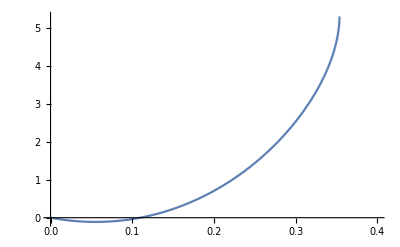

```mathematica
xf1[a_]:=Sqrt[1/4 (3-√(1-8 a^2)- √(2+8 a^2+2 √(1-8 a^2)))]
xf2[a_]:=Sqrt[1/4 (3-√(1-8 a^2)+ √(2+8 a^2+2 √(1-8 a^2)))]
xf3[a_]:=Sqrt[1/4 (3+√(1-8 a^2)- √(2+8 a^2-2 √(1-8 a^2)))]
xf4[a_]:=Sqrt[1/4 (3+√(1-8 a^2)+ √(2+8 a^2-2 √(1-8 a^2)))]
xf[a_] = xf4[a]
xf[a0]//FullSimplify
yf[a_]:=xf[a](xf[a]^2-1)/a
yf[a0]//FullSimplify

g[a_]=9*(xf[a]^2 - yf[a]^2)^2 - 4a//FullSimplify
g[a]//Expand
Plot[g[a], {a, 0, .4}]
```

```mathematica
Solve[g[a]==0, a]
```

{{a→0},{a→1/27 (4-239 (2/(-745+27 √75669))^(1/3)+(1/2 (-745+27 √75669))^(1/3))}}

```mathematica
Solve[g[a]==0, a]//N
```

{{a→0.},{a→0.109722}}

```mathematica
xf[a_] = xf1[a];
yf[a_]:=xf[a]*(xf[a]^2-1)/a//FullSimplify;
xf[a]^2
yf[a]^2//FullSimplify
M={{1 - 3x0^2, a},{-a, 1 - 3y0^2}}//FullSimplify;
M//MatrixForm
eig = Eigenvalues[M]//Simplify;
g[a]//Simplify
b=((-eig[[1]] + eig[[2]])/2)^2//Simplify;
b
Solve[b^2==0, a]
```

1/4 (3-√(1-8 a^2)-√(2+8 a^2+2 √(1-8 a^2)))

1/4 (3-√(1-8 a^2)+√(2+8 a^2+√(4-32 a^2)))

(1-3 x0^2 | a
-a | 1-3 y0^2)

1/2 (9+4 a (-2+9 a)-9 √(1-8 a^2))

1/4 (-4 a^2+9 (x0^2-y0^2)^2)

{{a→-3/2 (x0^2-y0^2)},{a→-3/2 (x0^2-y0^2)},{a→3/2 (x0^2-y0^2)},{a→3/2 (x0^2-y0^2)}}

```mathematica
eig
```

{1/2 (2-3 x0^2-3 y0^2-√(-4 a^2+9 (x0^2-y0^2)^2)),1/2 (2-3 x0^2-3 y0^2+√(-4 a^2+9 (x0^2-y0^2)^2))}